```mathematica
ExtendedGCD[4321,1234]//Print
```

{1,{309,-1082}}

```mathematica
?*Graph
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/ads/mm-images

```mathematica
SetDirectory["../images"]
```

/Users/ken_l/Documents/ads/images

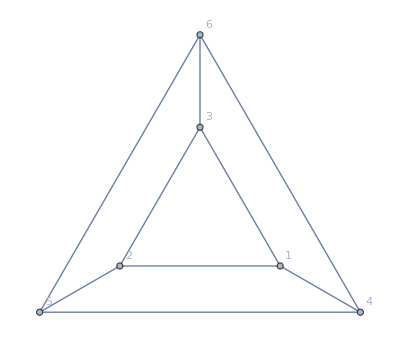
-Graphics-(a)

```mathematica
(p=PetersenGraph[3,2,VertexLabels->"Name",VertexLabelStyle->Large])//Labeled[#,Style["(a)",Large]]&
```

```mathematica
GraphDiameter[p]
```

2

```mathematica
GraphRadius[p]
```

2

```mathematica
GraphCenter[p]
```

{1,2,3,4,5,6}

```mathematica
PetersenGraph[3,2,VertexLabels->"Name",VertexLabelStyle->Large]//Labeled[#,Style["(a)",Large]]&//Export["fig-measure-graph-1.png",#,"PNG"]&
```

fig-measure-graph-1.png

```mathematica
(p=GridGraph[{3,4},VertexLabels->"Name",VertexLabelStyle->Large])//Labeled[#,Style["(b)",Large]]&//Export["fig-measure-graph-2.png",#,"PNG"]&
```

fig-measure-graph-2.png

```mathematica
?*Eccen*
```

```mathematica
{{#,VertexEccentricity[p,#]}&/@Range[12],GraphDiameter[p],
GraphRadius[p],
GraphCenter[p]}
```

{(1 | 5
2 | 4
3 | 5
4 | 4
5 | 3
6 | 4
7 | 4
8 | 3
9 | 4
10 | 5
11 | 4
12 | 5),5,3,{5,8}}

```mathematica
SeedRandom[3];
(p=RandomGraph[{8,14},GraphLayout->"CircularEmbedding",VertexLabels->"Name",VertexLabelStyle->Large])//Labeled[#,Style["(c)",Large]]&//Export["fig-measure-graph-3.png",#,"PNG"]&
```

fig-measure-graph-3.png

```mathematica
{{#,VertexEccentricity[p,#]}&/@Range[8],GraphDiameter[p],
GraphRadius[p],
GraphCenter[p]}
```

{(1 | 2
2 | 2
3 | 3
4 | 3
5 | 2
6 | 3
7 | 4
8 | 4),4,2,{1,2,5}}

```mathematica
(p=ButterflyGraph[2,2])//Labeled[#,Style["(d)",Large]]&//Export["fig-measure-graph-4.png",#,"PNG"]&
```

fig-measure-graph-4.png

```mathematica
{{#,VertexEccentricity[p,#]}&/@Range[8],GraphDiameter[p],
GraphRadius[p],
GraphCenter[p]}
```

{(1 | 4
2 | 4
3 | 4
4 | 4
5 | 4
6 | 4
7 | 4
8 | 4),4,4,{1,2,3,4,5,6,7,8,9,10,11,12}}

```mathematica
Directory[]
```

/Users/ken_l/Library/Mobile Documents/com~apple~CloudDocs/MATH.2190/FinalExamCalculations

```mathematica
done=False;k=78;
While[Not[done],k+=1;SeedRandom[k];G=RandomGraph[{10,15}];
{r,d}=G//{GraphRadius[#],GraphDiameter[#]}&;
If[0.6<(r/d)&&(r/d)<0.9,done=True]]
G//{GraphRadius[#],GraphDiameter[#]}&
```

{2,3}

```mathematica
m1=G//GraphDistanceMatrix//TeXForm//Print
```

\left(
\begin{array}{cccccccccc}
 0 & 2 & 1 & 2 & 2 & 3 & 3 & 2 & 1 & 1 \\
 2 & 0 & 1 & 2 & 3 & 3 & 3 & 2 & 3 & 2 \\
 1 & 1 & 0 & 1 & 2 & 2 & 2 & 1 & 2 & 1 \\
 2 & 2 & 1 & 0 & 3 & 3 & 3 & 2 & 3 & 2 \\
 2 & 3 & 2 & 3 & 0 & 2 & 1 & 1 & 2 & 1 \\
 3 & 3 & 2 & 3 & 2 & 0 & 1 & 1 & 3 & 2 \\
 3 & 3 & 2 & 3 & 1 & 1 & 0 & 1 & 3 & 2 \\
 2 & 2 & 1 & 2 & 1 & 1 & 1 & 0 & 2 & 1 \\
 1 & 3 & 2 & 3 & 2 & 3 & 3 & 2 & 0 & 1 \\
 1 & 2 & 1 & 2 & 1 & 2 & 2 & 1 & 1 & 0 \\
\end{array}
\right)

```mathematica
m2=G//GraphDistanceMatrix//TeXForm//Print
```

\left(
\begin{array}{cccccccccccc}
 0 & 2 & 2 & 2 & 3 & 3 & 3 & 1 & 2 & 3 & 1 & 1 \\
 2 & 0 & 2 & 2 & 1 & 1 & 1 & 3 & 2 & 1 & 1 & 3 \\
 2 & 2 & 0 & 1 & 3 & 2 & 1 & 2 & 2 & 3 & 1 & 1 \\
 2 & 2 & 1 & 0 & 3 & 1 & 2 & 1 & 2 & 3 & 2 & 1 \\
 3 & 1 & 3 & 3 & 0 & 2 & 2 & 4 & 3 & 2 & 2 & 4 \\
 3 & 1 & 2 & 1 & 2 & 0 & 2 & 2 & 3 & 2 & 2 & 2 \\
 3 & 1 & 1 & 2 & 2 & 2 & 0 & 3 & 3 & 2 & 2 & 2 \\
 1 & 3 & 2 & 1 & 4 & 2 & 3 & 0 & 3 & 4 & 2 & 2 \\
 2 & 2 & 2 & 2 & 3 & 3 & 3 & 3 & 0 & 1 & 3 & 1 \\
 3 & 1 & 3 & 3 & 2 & 2 & 2 & 4 & 1 & 0 & 2 & 2 \\
 1 & 1 & 1 & 2 & 2 & 2 & 2 & 2 & 3 & 2 & 0 & 2 \\
 1 & 3 & 1 & 1 & 4 & 2 & 2 & 2 & 1 & 2 & 2 & 0 \\
\end{array}
\right)

```mathematica
m1="\\left(\n\\begin{array}{cccccccccc}\n 0 & 2 & 1 & 2 & 2 & 3 & 3 & 2 & 1 & 1 \\\\\n 2 & 0 & 1 & 2 & 3 & 3 & 3 & 2 & 3 & 2 \\\\\n 1 & 1 & 0 & 1 & 2 & 2 & 2 & 1 & 2 & 1 \\\\\n 2 & 2 & 1 & 0 & 3 & 3 & 3 & 2 & 3 & 2 \\\\\n 2 & 3 & 2 & 3 & 0 & 2 & 1 & 1 & 2 & 1 \\\\\n 3 & 3 & 2 & 3 & 2 & 0 & 1 & 1 & 3 & 2 \\\\\n 3 & 3 & 2 & 3 & 1 & 1 & 0 & 1 & 3 & 2 \\\\\n 2 & 2 & 1 & 2 & 1 & 1 & 1 & 0 & 2 & 1 \\\\\n 1 & 3 & 2 & 3 & 2 & 3 & 3 & 2 & 0 & 1 \\\\\n 1 & 2 & 1 & 2 & 1 & 2 & 2 & 1 & 1 & 0 \\\\\n\\end{array}\n\\right)"
```

(0 | 2 | 1 | 2 | 2 | 3 | 3 | 2 | 1 | 1
2 | 0 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2
1 | 1 | 0 | 1 | 2 | 2 | 2 | 1 | 2 | 1
2 | 2 | 1 | 0 | 3 | 3 | 3 | 2 | 3 | 2
2 | 3 | 2 | 3 | 0 | 2 | 1 | 1 | 2 | 1
3 | 3 | 2 | 3 | 2 | 0 | 1 | 1 | 3 | 2
3 | 3 | 2 | 3 | 1 | 1 | 0 | 1 | 3 | 2
2 | 2 | 1 | 2 | 1 | 1 | 1 | 0 | 2 | 1
1 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 0 | 1
1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 0)

```mathematica
TuranGraph[9,3]//GraphDistanceMatrix
```

(0 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 0 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1
1 | 1 | 1 | 2 | 0 | 2 | 1 | 1 | 1
1 | 1 | 1 | 2 | 2 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 2
1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 0)